## PRÁCTICA 2 - AUTÓMATAS CELULARES

## Luis José Ferrer Estellés Diana Bachynska Grupo 3 C021

# Ejercicio 1

```mathematica
ListaRegla[n_]:= Module[{numBin, listaR, dividendo, cociente, div, result, resto,i},

numBin={};
listaR= {{0,0,0},{0,0,1},{ 0,1,0}, {0,1,1} ,{1,0,0}, {1,0,1}, {1,1,0},{ 1,1,1}};
dividendo= n;

While[dividendo>=2,
div= QuotientRemainder[dividendo,2];
cociente=div[[1]];
resto=div[[2]];(*accedemos al resto de la división*)
AppendTo[numBin, resto];(*el resto se va añadiendo de derecha a izquierda*)
dividendo=cociente;
];
AppendTo[numBin,dividendo];
numBin=PadRight[numBin,8]; (*el 8 indica que quiero que mi lista tenga longitud 8*)
result = {};
For[i=1, i<= 8, i++,
AppendTo[result,Append[listaR[[i]],numBin[[i]]]];
];
Return[result];
]
```

```mathematica
ListaRegla[54]
```

{{0,0,0,0},{0,0,1,1},{0,1,0,1},{0,1,1,0},{1,0,0,1},{1,0,1,1},{1,1,0,0},{1,1,1,0}}

```mathematica
configuracionSig[confActual_,regla_]:=Module[{n,confSiguiente,i,estadoIzq,estadoActual,estadoDer,reglaAplicable,reglas, indexRegla,res,q, x},
n=Length[confActual];
reglas = ListaRegla[regla];
(*Print [reglas];*)
indexRegla = Cases[reglas,{confActual[[n]], confActual[[1]], confActual[[2]],x_}-> x];
res = indexRegla;
Print[res];

For[i=2,i<n,i++,
indexRegla=Cases[reglas,{confActual[[i-1]], confActual[[i]], confActual[[i+1]],x_}-> x];
AppendTo[res,indexRegla];
];
     
indexRegla = Cases[reglas,{confActual[[n-1]], confActual[[n]], confActual[[1]],x_}->x];
AppendTo[res,indexRegla];

Return[Flatten[res]];
]
```

```mathematica
configuracionSig[{1,0,1,1,0,1}, 54]
```

{0}

{0,1,0,0,1,0}

```mathematica
AC[Inicial_List,Regla_Integer,t_Integer]:=Module[{ListRegla, configSig, i, res, aux},
(*ListRegla = ListaRegla[Regla];*)
aux = Inicial;
res = {aux};
For[i=1, i<t, i++,
aux = configuracionSig[res[[i]], Regla];
Print[aux];
AppendTo[res, aux];
];
ArrayPlot[res]
]
```

{0}

{0,1,1,1,0}

{1}

{1,0,0,0,1}

{0}

{0,1,0,1,0}

{1}

{1,1,1,1,1}

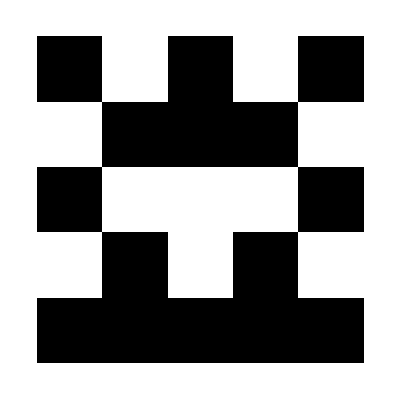

```mathematica
AC[{1, 0, 1, 0, 1}, 54, 5]
```

# Ejercicio 2

```mathematica
actualizarCelda[rejilla_,k_,x_,y_]:=Module[{vecinos,conteo},
vecinos=rejilla[[Mod[{x-1,x,x+1}-1,k]+1,Mod[{y-1,y,y+1}-1,k]+1]];
conteo=Total[Flatten[vecinos]]-rejilla[[x,y]];
If[rejilla[[x,y]]==1,
If[conteo==2||conteo==3,1,0],
If[conteo==3,1,0]
(*If[conteo==3||(conteo==2&&rejilla[[x,y]]==1),1,0]*)

]
];
```

```mathematica
SimulacionJuegoDeLaVida[R_,k_Integer,n_Integer]:=Module[{rejilla=R,siguienteRejilla},
Table[siguienteRejilla=Table[actualizarCelda[rejilla,k,i,j],{i,1,k},{j,1,k}];
rejilla=siguienteRejilla;
ArrayPlot[rejilla,
Mesh->True,
ImageSize->Large,
PlotRangePadding->None,
Frame->False,
ColorRules->{0->White,1->Black}],{n}
]
];
```

```mathematica
RInicial={{0,1,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{1,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}};
resultados=SimulacionJuegoDeLaVida[RInicial,5,5];
ListAnimate[resultados]
```

## Parte II - AUTÓMATAS CELULARES

# Ejercicio 1

```mathematica
Ej1[afd_]:=Module[{q,sigma,delta,q0,F,s,f,splus,aux,vecinos,i,k, AC},
q=afd[[1]];(*estados*)
sigma=afd[[2]]; (*alfabeto*)
delta=afd[[3]];  (*transiciones*)
q0=afd[[4]];  (*estado inicial*)
F=afd[[5]]; (*estados finales o de aceptación*)

splus=F; 
vecinos={};
     AC={};

vecinos=Join[
Flatten[Table[{q[[i]],q[[k]],q[[k]]},{i,Length[q]},{k,Length[q]}],1],(*Combinaciones de estados*)Flatten[Table[{sigma[[i]],sigma[[k]],sigma[[k]]},{i,Length[sigma]},{k,Length[sigma]}],1],(*Combinaciones de símbolos*)delta];

s = Union[q,sigma];
AC={s,vecinos,splus};
Return [AC];
]
```

```mathematica
automata = {{q,p,r},{a,b},{{q,a,p},{q,b,r},{p,a,r},{p,b,q},{r,a,r},{r,b,r}},q,{r}}
Ej1[automata]
```

{{q,p,r},{a,b},{{q,a,p},{q,b,r},{p,a,r},{p,b,q},{r,a,r},{r,b,r}},q,{r}}

{{a,b,p,q,r},{{q,q,q},{q,p,p},{q,r,r},{p,q,q},{p,p,p},{p,r,r},{r,q,q},{r,p,p},{r,r,r},{a,a,a},{a,b,b},{b,a,a},{b,b,b},{q,a,p},{q,b,r},{p,a,r},{p,b,q},{r,a,r},{r,b,r}},{r}}

# Ejercicio 2

```mathematica
Ej2[cadena_,AC_,q_]:=Module[{s,f,splus,len,i,destino, diagrama, secuencia },s=AC[[1]];
f=AC[[2]];
splus=AC[[3]];
len=Length[cadena];
destino=Prepend[cadena,q];
If[ Length[f[[1]]]==4,
destino=Append[destino,q]];
For[i=1,i<=len,i++,
destino=SiguienteConf4[f,destino];
Print[destino];
If[destino===False,
Return[False]
];
];

Return[MemberQ[splus,destino[[len+1]]]];
];
```

```mathematica
SiguienteConf4[f_,estado_]:=Module[{bidireccional,est,reg,len,destino,i,aux},
bidireccional=Length[f[[1]]]==4;
est=estado;
reg=f;
len=Length[est];
destino={};
If[bidireccional,
destino={est[[1]]};
For[i=2,i<len,i++,
aux=Cases[reg,{est[[i-1]],est[[i]],est[[i+1]],_}];
If[aux=!={},
aux=Flatten[aux];
AppendTo[destino,aux[[4]]],
Return[False]
];
];
AppendTo[destino,est[[len]]
];,
destino={est[[1]]};
For[i=2,i<=len,i++,
aux=Cases[reg,{est[[i-1]],est[[i]],_}];
If[aux=!={},
aux=Flatten[aux];
AppendTo[destino,aux[[3]]],
Return[False]];
];
];
Return[destino];
];
```

```mathematica
AC ={{a,b,p,q,r},{{q,q,q},{q,p,p},{q,r,r},{p,q,q},{p,p,p},{p,r,r},{r,q,q},{r,p,p},{r,r,r},{a,a,a},{a,b,b},{b,a,a},{b,b,b},{q,a,p},{q,b,r},{p,a,r},{p,b,q},{r,a,r},{r,b,r}},{r}};
Ej2[{a,b,a,a,b}, AC, q]
```

{q,p,b,a,a,b}

{q,p,q,a,a,b}

{q,p,q,p,a,b}

{q,p,q,p,r,b}

{q,p,q,p,r,r}

True

```mathematica
AC ={{a,b,p,q,r},{{q,q,q},{q,p,p},{q,r,r},{p,q,q},{p,p,p},{p,r,r},{r,q,q},{r,p,p},{r,r,r},{a,a,a},{a,b,b},{b,a,a},{b,b,b},{q,a,p},{q,b,r},{p,a,r},{p,b,q},{r,a,r},{r,b,r}},{r}};
Ej2[{a,b,a}, AC, q]
```

{q,p,b,a}

{q,p,q,a}

{q,p,q,p}

False

```mathematica
AC={{a,b,p,q,r},{{q,q,q,q},{q,p,p,p},{q,r,r,r},{p,q,q,q},{p,p,p,p},{p,r,r,r},{r,q,q,q},{r,p,p,p},{r,r,r,r},{a,a,a,a},{a,b,b,b},{b,a,a,a},{b,b,b,b},{q,a,p,p},{q,b,r,r},{a,b,a,p},{a,b,q,r},{p,a,r,r},{p,b,q,q},{r,a,r,r},{r,b,r,r},{q,b,q,r},{q,a,q,r},{q,a,b,a}},{r}};
Ej2[{a,b,a},AC,q]
```

False

False

```mathematica
AC={{a,b,p,q,r},{{q,q,q,q},{q,p,p,p},{q,r,r,r},{p,q,q,q},{p,p,p,p},{p,r,r,r},{r,q,q,q},{r,p,p,p},{r,r,r,r},{a,a,a,a},{a,b,b,b},{b,a,a,a},{b,b,b,b},{q,a,p,p},{q,b,r,r},{a,b,a,p},{a,b,q,r},{p,a,r,r},{p,b,q,q},{r,a,r,r},{r,b,r,r},{q,b,q,r},{q,a,q,r},{q,a,b,a}},{r}};
Ej2[{a},AC,q]
```

{q,r,q}

True

# Ejercicio 3

```mathematica
MuestraSecuencia[cadena_,AC_,q_]:=Module[{f,splus,secuencia,diagrama,destino,i,bidireccional},
f=AC[[2]];
splus=AC[[3]];
bidireccional=Length[f[[1]]]==4;
destino=Prepend[cadena,q];
If[bidireccional,destino=Append[destino,q]];
secuencia={destino};
For[i=1,i<=Length[cadena],i++,
destino=SiguienteConf4[f,destino];
If[destino===False,Break[]];
AppendTo[secuencia,destino];];
secuencia=Reverse[secuencia];
diagrama=ArrayPlot[secuencia,Mesh->True,ColorRules->{a->Red,b->Blue,q->Yellow,p->Purple,r->LightGreen}];
diagrama
]
```

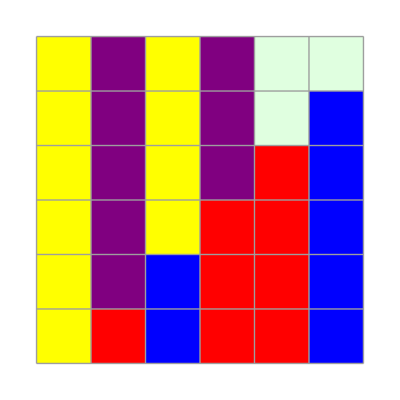

```mathematica
AC = {{a,b,p,q,r},{{q,q,q},{q,p,p},{q,r,r},{p,q,q},{p,p,p},{p,r,r},{r,q,q},{r,p,p},{r,r,r},{a,a,a},{a,b,b},{b,a,a},{b,b,b},{q,a,p},{q,b,r},{p,a,r},{p,b,q},{r,a,r},{r,b,r}},{r}};
MuestraSecuencia[{a,b,a,a,b}, AC, q]
```

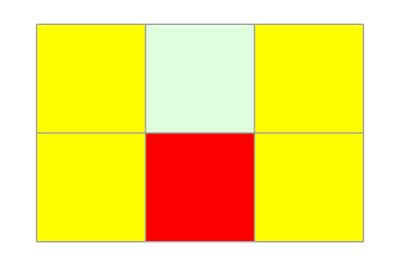

```mathematica
AC={{a,b,p,q,r},{{q,q,q,q},{q,p,p,p},{q,r,r,r},{p,q,q,q},{p,p,p,p},{p,r,r,r},{r,q,q,q},{r,p,p,p},{r,r,r,r},{a,a,a,a},{a,b,b,b},{b,a,a,a},{b,b,b,b},{q,a,p,p},{q,b,r,r},{a,b,a,p},{a,b,q,r},{p,a,r,r},{p,b,q,q},{r,a,r,r},{r,b,r,r},{q,a,q,r}},{r}};
AC={{a,b,p,q,r},{{q,q,q,q},{q,p,p,p},{q,r,r,r},{p,q,q,q},{p,p,p,p},{p,r,r,r},{r,q,q,q},{r,p,p,p},{r,r,r,r},{a,a,a,a},{a,b,b,b},{b,a,a,a},{b,b,b,b},{q,a,p,p},{q,b,r,r},{a,b,a,p},{a,b,q,r},{p,a,r,r},{p,b,q,q},{r,a,r,r},{r,b,r,r},{q,b,q,r},{q,a,q,r},{q,a,b,a}},{r}};
MuestraSecuencia[{a},AC,q]
```